# SCQ-Magnon Coupling in MANR

```mathematica
ClearAll["Global`*"]
```

```mathematica
Directory[]
```

C:\Users\jeffc\Documents

## Global Functions

```mathematica
ZeroMatrix2N[N_]:=
Module[{N0=N,H},
H=Table[0,{2N0},{2N0}];
H
]

MANRMatrix2N[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_]:=
Module[{H,N0=N,W,X,Y,Z},
H=ZeroMatrix2N[N0];

Quiet[Do[
H[[2+2(i-1)-1,2+2(i-1)]]=W;
H[[2+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,2+2(i-1)]]];

(*H[[3+2(i-1)-1,3+2(i-1)]]=X;
H[[3+2(i-1),3+2(i-1)-1]]=Conjugate[H[[3+2(i-1)-1,3+2(i-1)]]];
H[[2+2(i-1)-1,4+2(i-1)]]=X;
H[[4+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,4+2(i-1)]]];*)

H[[3+2(i-1)-1,3+2(i-1)]]=X;
H[[3+2(i-1),3+2(i-1)-1]]=Conjugate[H[[3+2(i-1)-1,3+2(i-1)]]];
H[[2+2(i-1)-1,4+2(i-1)]]=Conjugate[X];
H[[4+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,4+2(i-1)]]];

H[[2+2(i-1)-1,3+2(i-1)]]=Y;
H[[3+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,3+2(i-1)]]];
H[[2+2(i-1),4+2(i-1)]]=Conjugate[Y];
H[[4+2(i-1),2+2(i-1)]]=Conjugate[H[[2+2(i-1),4+2(i-1)]]];

H[[2+2(i-1)-1,5+2(i-1)]]=Z;
H[[5+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,5+2(i-1)]]];
H[[2+2(i-1),6+2(i-1)]]=Conjugate[Z];
H[[6+2(i-1),2+2(i-1)]]=Conjugate[H[[2+2(i-1),6+2(i-1)]]];

H[[i,i]]=3 J1 s +6J2 s +h+κ+(-1)^i Δκ;

W=-J1 s E^(ⅈ ξ);
X=-J1 s E^(ⅈ ξ/2);
Y=-2s √(DM^2+J2^2) E^(ⅈ ϕ) Cos[3/2 ξ];
Z=-s √(DM^2+J2^2)E^(-ⅈ ϕ);

,{i,1,2N0}];];
H[[1,1]]=H[[1,1]]-J1 s-3J2 s;
H[[2,2]]=H[[2,2]]-J1 s-3J2 s;
H[[3,3]]=H[[3,3]]-J2 s;
H[[4,4]]=H[[4,4]]-J2 s;
H[[2N0,2 N0]]=H[[2N0,2 N0]]-J1 s-3J2 s;
H[[2N0-1,2 N0-1]]=H[[2N0-1,2 N0-1]]-J1 s-3J2 s;
H[[2N0-2,2 N0-2]]=H[[2N0-2,2 N0-2]]-J2 s;
H[[2N0-3,2 N0-3]]=H[[2N0-3,2 N0-3]]-J2 s;
H
]

DyadG[x_,y_,z_,x1_,y1_,z1_]:=
Module[{DG,G},
G=1/(√((x-x1)^2+(y-y1)^2+(z-z1)^2));
DG=({{D[D[G,x1],x], D[D[G,y1],x], D[D[G,z1],x]}, {D[D[G,x1],y], D[D[G,y1],y], D[D[G,z1],y]}, {D[D[G,x1],z], D[D[G,y1],z], D[D[G,z1],z]}});
DG
]

UMatrix[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_]:=
Module[{N0=N,H,sortorder,U},
H=MANRMatrix2N[J1,J2,DM,s,κ,Δκ,h,ϕ,ξ,N0];
sortorder=Ordering[Eigensystem[H][[1]]];
U=Chop[Eigensystem[H][[2]][[sortorder]]];
U
]

MANRCouplingDiscrete[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,Num_,m_,x_,y_,z_,sum1_,sum2_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g,β,n},
x1=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
U=UMatrix[J1,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];

g=(√3 3)/4 Norm[NIntegrate[Sum[(E^(ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],1]+E^(-ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],2]+E^(-ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],3]+E^(ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],0])*((3 (-x1[[M]]+x)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2))+(3 (-y1+y)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2)))E^(ⅈ ξ y1),{y1,sum1,sum2,3},{M,1,2Num}],{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}]];

Chop[g]
]
```

## Global Parameters & Constants

### System Parameters

```mathematica
a=4*10^-10 (*lattice spacing; dim: L, units: m*);
J=2; (*NN exchange coupling; dim: energy, units: eV*)
h=0.05; (*Zeeman spliting h=Subscript[gμ, B] B where g=2 for electrons; dim: energy, units eV*)
J2=0.15; (*NNN exchange coupling; dim: energy, units: eV*)
s=3/2; (*Sz quantum number; dimensionless*)
DM=0.3; (*NNN DMI; dim: energy, units eV*)
κ=0; (*Easy-axis anisotropy; dim: energy, units: eV*)
ϕ=ArcTan[DM/J2](*Pi/2*); (*Magnetic flux; dimensionless*)
ℏ=6.582*10^-1; (*Planck's constant; units: meV/THz*)
Ms=(3/2 μB s)/(a^2 w); (*Saturation magnetization; units: *)
w=10^-10;(*width of ferromagnetic film; units: m*)
```

### Physical Constants

```mathematica
kb=8.6*10^-2; (*Boltzmann constant; meV*)

γe=1.76*10^11;(*electron gyromagnetic ratio; rad*s^-1*T^-1*)
μ0=4Pi*10^-7;(*permeability of free space; N/m^2*)
μB=9.274*10^-24 (*Bohr magneton; J*T^-1*);
```

### Computational Settings

```mathematica
WP=60; (*Working Precision*)
AG=10; (**)
```

## Dispersion

```mathematica
NSamp = 500; (*Number of sample points*)
Num=59; (*Half the number of bands*)
Δκ=0; (*Difference in easy-axis anisotropy*)

f[ξ_]:=
Module[{H,sortorder,dumH},
H=MANRMatrix2N[J,J2,DM,s,0,Δκ,h,ϕ,ξ,Num];
dumH=Eigenvalues[H];(*eigenvalues*)
sortorder=Ordering[dumH];(*This orders the eigenvalues and eigenfunctions accordingly*)

Table[{ξ ,(dumH[[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}]
]

Dispersion = ParallelMap[f,Table[-Pi/3+j* N[(2 Pi/3)/NSamp],{j,0,NSamp}]];//AbsoluteTiming
```

{8.42567,Null}

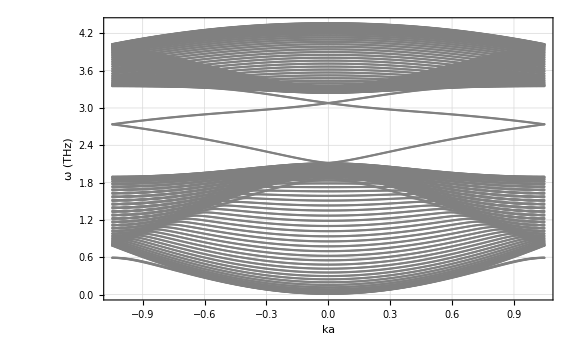

```mathematica
ListPlot[Dispersion,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Gray,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,GridLines->{}]
```

## Wavefunction Algorithm

```mathematica
(*Calculate table of values*)
WaveAlgo[J_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,Num_,Naux_,upperbound_,lowerbound_]:=
Module[{N0=Num,NBand=Naux,A},

Do[
ξ=-Pi/3+j* N[(2 Pi/3)/Naux];

H=MANRMatrix2N[J,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];

A=Eigensystem[H];

sortorder=Ordering[A[[1]]];

f[ξ]=Table[{ξ ,(A[[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}];

(*Fun[l_]:=Table[f[ξ][[l]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}];*)

(*Iterates through table of values to grab indices which coincide to bands within desired bounds*)
FindIndices[NBand_,N0_,ub_,lb_]:=
Module[{EmptyList,Indices},
EmptyList={};

Do[
Do[
If[lb<Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/NBand]}][[j]]<ub, AppendTo[EmptyList,i]]
,{j,1,Length[Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/NBand]}]]}]
,{i,1,2N0}];

Indices=DeleteDuplicates[EmptyList];
Indices
];

BandIndices=FindIndices[Naux,Num,upperbound,lowerbound];

(*Find k value and corresponding band index for a fixed energy*)
FindMom[ω_,err_]:=
Module[{EmptyList,Mom},
EmptyList={};

Do[
Do[
If[ω-err<Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]<ω+err, AppendTo[EmptyList,{BandIndices[[i]],Table[f[ξ][[BandIndices[[i]]]][[1]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]],Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]}]]
,{j,1,Length[Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}]]}]
,{i,1,Length[BandIndices]}];

Mom=Sort[EmptyList,Abs[#1[[1]]]<Abs[#2[[1]]]&] (*Sorts list from smallest to largest absolute momentum*)
];

(*Takes the mean value of closely separated k values*)
MeanMom[ω_,err_]:=
Module[{MomList,DeleteMomList,EmptyList},

MomList=Split[FindMom[ω,err],Abs[#1[[2]]-#2[[2]]]<err&&#1[[1]]==#2[[1]]&];
EmptyList={};

For[i=1,i<Length[MomList]+1,i++,AppendTo[EmptyList,Mean[MomList[[i]]]]];

EmptyList
];

(*Calculates the wavefunction for impure spin lattice*)
(*NOTE: I changed the x recurrence table to sum in steps of 1/2 instead of √3/2*)
wavefunctions[ω_,err_,N0]:=
Module[{wavefunction,U,f,k,band,β,n,x},
wavefunction={};

Do[
k=MeanMom[ω,err][[j]][[2]];
band=MeanMom[ω,err][[j]][[1]];
U=UMatrix[J,J2,DM,s,κ,Δκ,h,ϕ,k,Num];
x=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
f=Table[{x[[M]] *a/10^-9,Abs[U[[band]][[M]]]^2},{M,1,2Num}];
AppendTo[wavefunction,f]
,{j,1,Length[MeanMom[ω,err]]}];

wavefunction

];

];
```

## Coupling

```mathematica
NSamp=300;
Num=59;
NSteps=59;
Δκ=0;
κ=0;
upperbound=3.2;
lowerbound=2.1;
l=(((√3)/2)*(Num-1))*a;
(*l=(3/2)*2*Num*a;*)
d=12.5;
y=0;
F=(γe/(2Pi))*(μ0/(√a))*√((3μB Ms)/(2l w))*10^-3
ω=2.4+κ/(2Pi ℏ);
error=1/NSamp;
(*WaveAlgo[J,J2,DM,s,κ,Δκ,h,ϕ,Num,NSamp,upperbound,lowerbound];*)

(*CouplingList = {};
momma=MeanMom[ω,error];
Do[

numba=momma[[j]][[1]];
mom=momma[[j]][[2]];

g[x_]:=Module[{g},
g=F*MANRCouplingDiscrete[J,J2,DM,s,κ,Δκ,h,ϕ,mom,Num,numba,x,y,d,-3*300,3*300];
g
];

G=ParallelMap[g,Table[-20+j*N[(l/a+40)/NSteps],{j,0,NSteps}]];
AppendTo[CouplingList,G];
,{j,1,Length[momma]}]*)
```

5.28868×10^6

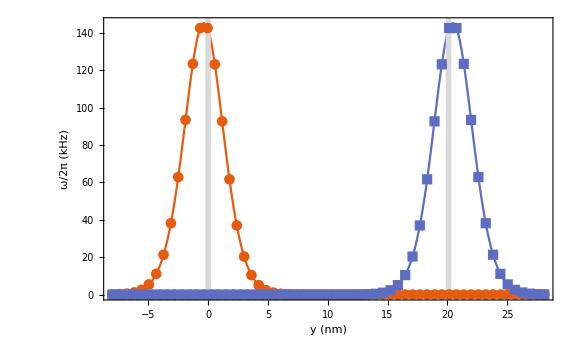

```mathematica
CouplingList;
Xtest = Table[-20+j*N[(l/a+40)/NSteps],{j,0,NSteps}]*0.4;
ListLinePlot[Table[Table[{Xtest[[i]],CouplingList[[j]][[i]]},{i,1,Length[Xtest]}],{j,1,Length[CouplingList]}],PlotMarkers->Automatic,InterpolationOrder->3,PlotTheme->"Scientific",FrameStyle->Thickness[0.005],GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],ImageSize->Large,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->32}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotRange->All]
```

## Coupling Density

Import::nffil: File MANR_Couple_Data/MANR_pure_couple_w=2.4.mx not found during Import.

Import::nffil: File MANR_Couple_Data/MANR_pure_couple_w=2.42.mx not found during Import.

Import::nffil: File MANR_Couple_Data/MANR_pure_couple_w=2.45.mx not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

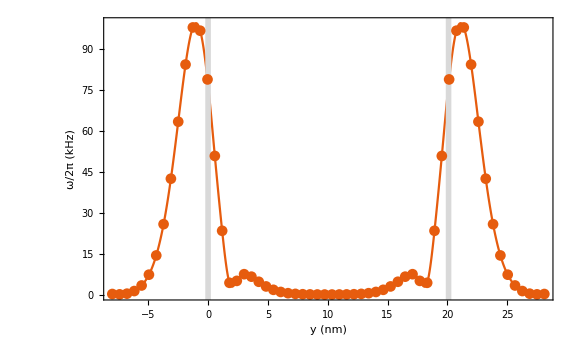

```mathematica
NSteps=59;
l=(((√3)/2)*(NSteps-1))*a;
MANRCoupleFreq=Table[Import["MANR_Couple_Data/MANR_pure_coupling_w="<>ToString[j]<>".mx"],{j,2.14,2.4,0.01}];
MANRCoupleFreq2=Table[Import["MANR_Couple_Data/MANR_pure_couple_w="<>ToString[j]<>".mx"],{j,2.4,3.2,0.01}];
MANRCoupleFreq=Join[MANRCoupleFreq,DeleteCases[MANRCoupleFreq2,_?FailureQ]];
x=Table[-20+j*N[(l/a+40)/NSteps],{j,0,NSteps}]*0.4;
```

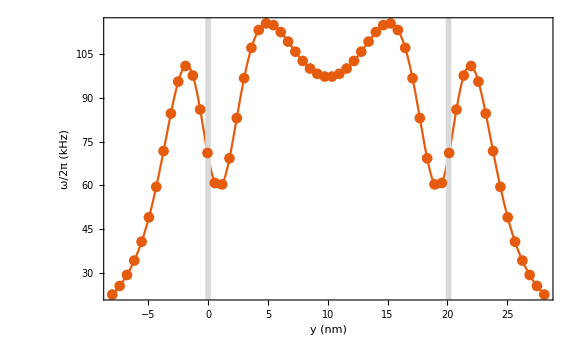

```mathematica
ListLinePlot[Table[{x[[i]],Total[MANRCoupleFreq[[90]]][[i]]},{i,1,Length[x]}],PlotMarkers->Automatic,InterpolationOrder->3,PlotTheme->"Scientific",FrameStyle->Thickness[0.005],GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],ImageSize->Large,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->32}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotRange->All]
```

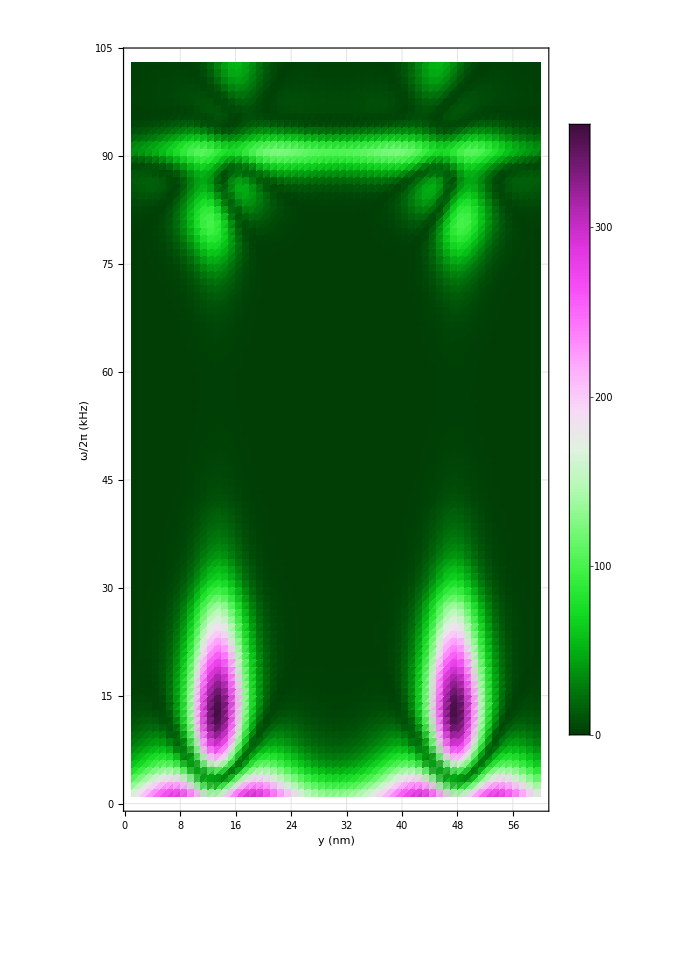

```mathematica
MANRCoupleFreqTotal=Table[Table[Total[MANRCoupleFreq[[j]]][[i]],{i,1,Length[x]}],{j,1,Length[MANRCoupleFreq]}];
ListDensityPlot[MANRCoupleFreqTotal,PlotTheme->"Scientific",FrameStyle->Thickness[0.005],GridLines->{},ImageSize->Large,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->32}],FrameLabel->{"y (nm)","ω/2π (kHz)"},AspectRatio->100/60,PlotRange->All,MaxPlotPoints->5000,ColorFunction->"GreenPinkTones"]
(*ListPlot3D[MANRCoupleFreqTotal,PlotTheme->"Scientific",ImageSize->Large,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->32}],PlotRange->All]*)
```

# Impurity Coupling in MANRs

## Functions

```mathematica
ImpureMANRMatrix2N[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_]:=
Module[{H,N0=N,W,X,Y,Z},
H=ZeroMatrix2N[N0];

Quiet[Do[
H[[2+2(i-1)-1,2+2(i-1)]]=W;
H[[2+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,2+2(i-1)]]];

H[[3+2(i-1)-1,3+2(i-1)]]=X;
H[[3+2(i-1),3+2(i-1)-1]]=Conjugate[H[[3+2(i-1)-1,3+2(i-1)]]];
H[[2+2(i-1)-1,4+2(i-1)]]=Conjugate[X];
H[[4+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,4+2(i-1)]]];

H[[2+2(i-1)-1,3+2(i-1)]]=Y;
H[[3+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,3+2(i-1)]]];
H[[2+2(i-1),4+2(i-1)]]=Conjugate[Y];
H[[4+2(i-1),2+2(i-1)]]=Conjugate[H[[2+2(i-1),4+2(i-1)]]];

H[[2+2(i-1)-1,5+2(i-1)]]=Z;
H[[5+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,5+2(i-1)]]];
H[[2+2(i-1),6+2(i-1)]]=Conjugate[Z];
H[[6+2(i-1),2+2(i-1)]]=Conjugate[H[[2+2(i-1),6+2(i-1)]]];

H[[i,i]]=3 J1 s +6J2 s +h+(-1)^i κ;

W=-J1 s E^(ⅈ ξ);
X=-J1 s E^(ⅈ ξ/2);
Y=-2s √(DM^2+J2^2) E^(ⅈ ϕ) Cos[3/2 ξ];
Z=-s √(DM^2+J2^2)E^(-ⅈ ϕ);

,{i,1,2N0}];];

(*Edge effects*)
H[[1,1]]=H[[1,1]]-J1 s-3J2 s;
H[[2,2]]=H[[2,2]]-J1 s-3J2 s;
H[[3,3]]=H[[3,3]]-J2 s;
H[[4,4]]=H[[4,4]]-J2 s;
H[[2N0,2 N0]]=H[[2N0,2 N0]]-J1 s-3J2 s;
H[[2N0-1,2 N0-1]]=H[[2N0-1,2 N0-1]]-J1 s-3J2 s;
H[[2N0-2,2 N0-2]]=H[[2N0-2,2 N0-2]]-J2 s;
H[[2N0-3,2 N0-3]]=H[[2N0-3,2 N0-3]]-J2 s;

N0=N0+1;

(*Onsite impurity effects*)
H[[N0-1,N0-1]]=0;

H[[N0-2,N0-2]]=H[[N0-2,N0-2]]-J1 s;
H[[N0,N0]]=H[[N0,N0]]-J1 s;
H[[N0+2,N0+2]]=H[[N0+2,N0+2]]-J1 s;

H[[N0-5,N0-5]]=H[[N0-5,N0-5]]-J2 s;
H[[N0-3,N0-3]]=H[[N0-3,N0-3]]-2J2 s;
H[[N0+3,N0+3]]=H[[N0+3,N0+3]]-J2 s;
H[[N0+1,N0+1]]=H[[N0+1,N0+1]]-2J2 s;

(*NN Impurity effects*)
H[[N0-1,N0]]=H[[N0-1,N0]]+J1 s E^(ⅈ ξ);
H[[N0,N0-1]]=Conjugate[H[[N0-1,N0]]];
H[[N0-1,N0-2]]=H[[N0-1,N0-2]]+J1 s E^(-ⅈ ξ/2);
H[[N0-2,N0-1]]=Conjugate[H[[N0-1,N0-2]]];
H[[N0-1,N0+2]]=H[[N0-1,N0+2]]+J1 s E^(-ⅈ ξ/2);
H[[N0+2,N0-1]]=Conjugate[H[[N0-1,N0+2]]];


(*NNN Impurity effects*)
H[[N0-3,N0-1]]=H[[N0-3,N0-1]]+2s √(DM^2+J2^2) E^(ⅈ ϕ) Cos[3/2 ξ];
H[[N0-1,N0-3]]=Conjugate[H[[N0-3,N0-1]]];
H[[N0-1,N0+1]]=H[[N0-1,N0+1]]+2s √(DM^2+J2^2) E^(ⅈ ϕ) Cos[3/2 ξ];
H[[N0+1,N0-1]]=Conjugate[H[[N0-1,N0+1]]];
H[[N0-5,N0-1]]=H[[N0-5,N0-1]]+s √(DM^2+J2^2)E^(-ⅈ ϕ);
H[[N0-1,N0-5]]=Conjugate[H[[N0-5,N0-1]]];
H[[N0-1,N0+3]]=H[[N0-1,N0+3]]+s √(DM^2+J2^2)E^(-ⅈ ϕ);
H[[N0+3,N0-1]]=Conjugate[H[[N0-1,N0+3]]];

H
]


ImpureUMatrixMANR[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_]:=
Module[{N0=N,H,sortorder,U},
H=ImpureMANRMatrix2N[J,J2,DM,s,κ,h,ϕ,ξ,N0];
sortorder=Ordering[Eigensystem[H][[1]]];
U=Chop[Eigensystem[H][[2]][[sortorder]]];
U
]

ImpureMANRCouplingDiscrete[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,Num_,m_,x_,y_,z_,sum1_,sum2_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g,β,n},
x1=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
U=ImpureUMatrixMANR[J1,J2,DM,s,κ,h,ϕ,ξ,Num];

g=(√3 3)/4 Norm[NIntegrate[Sum[(E^(ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],1]+E^(-ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],2]+E^(-ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],3]+E^(ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],0])*(-(3 (-x1[[M]]+x)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2))+(3 (-y1+y)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2)))E^(ⅈ ξ y1),{y1,sum1,sum2,3},{M,1,2Num}],{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}]];

Chop[g]
]
```

## Dispersion

```mathematica
NSamp = 1000; (*Number of sample points*)
Num=101; (*Half the number of bands*)
Δκ=0; (*Difference in easy-axis anisotropy*)

fImpure[ξ_]:=
Module[{H,sortorder,dumH},
H=ImpureMANRMatrix2N[J,J2,DM,s,κ,h,ϕ,ξ,Num];
dumH=Eigenvalues[H];(*eigenvalues*)
sortorder=Ordering[dumH];(*This orders the eigenvalues and eigenfunctions accordingly*)

Table[{ξ ,(dumH[[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}]
]

ImpureDispersion = ParallelMap[fImpure,Table[-Pi/3+j* N[(2 Pi/3)/NSamp],{j,0,NSamp}]];//AbsoluteTiming

ListPlot[ImpureDispersion,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Gray,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,GridLines->{}]
```

{9.721,Null}

-Graphics-

## Coupling Density

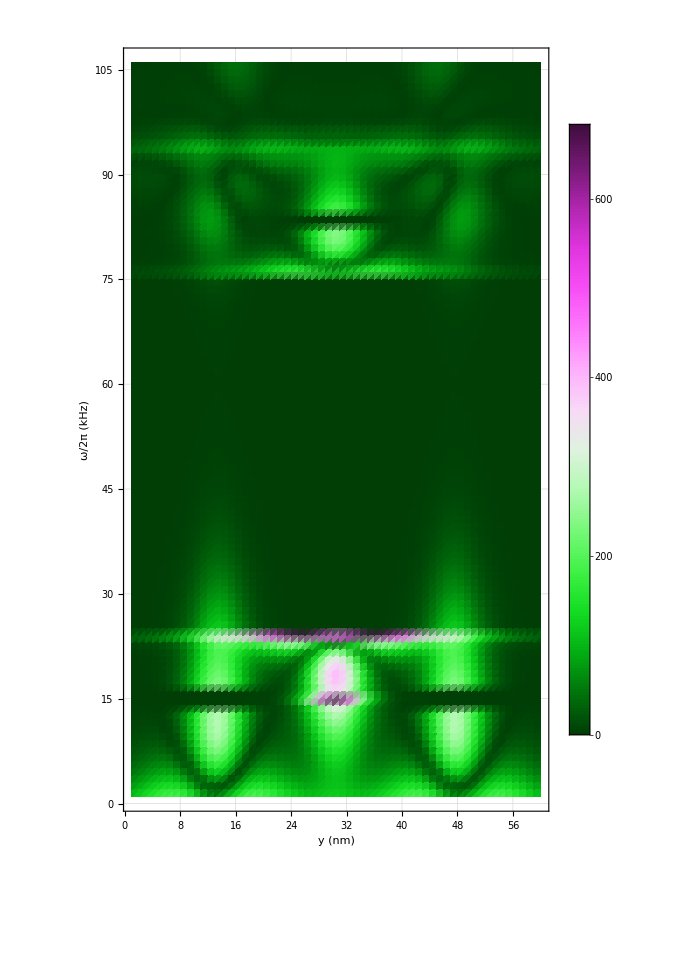

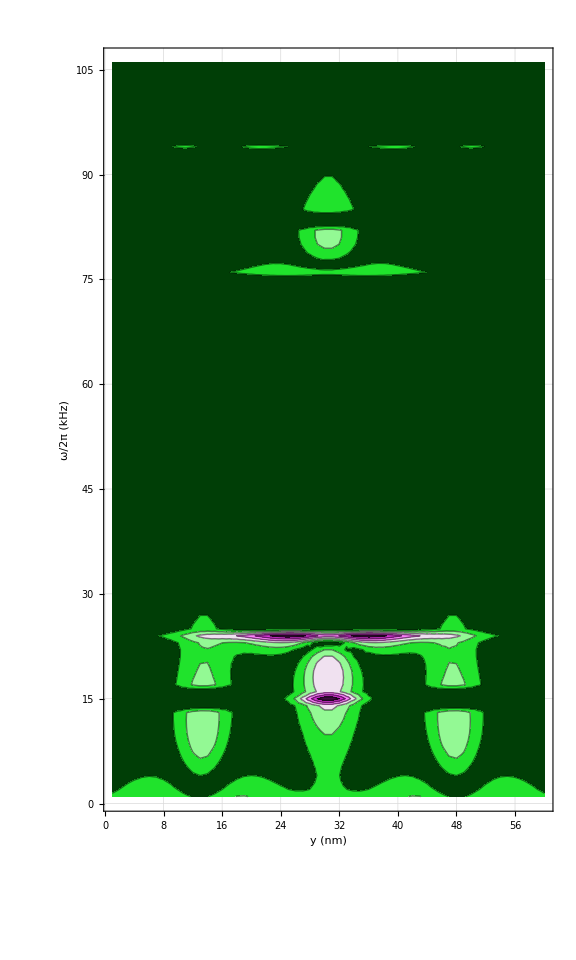

-Graphics3D-

```mathematica
NSteps=59;
l=(((√3)/2)*(NSteps-1))*a;
x=Table[-20+j*N[(l/a+40)/NSteps],{j,0,NSteps}]*0.4;
MANRImpureCoupleFreq=DeleteCases[Table[Import["MANR_impure_couple_data2/MANR_impure_couple_w="<>ToString[j]<>".mx"],{j,2.15,3.2,0.01}],_?FailureQ];//Quiet
MANRImpureCoupleFreqTotal=Table[Table[Total[MANRImpureCoupleFreq[[j]]][[i]],{i,1,Length[x]}],{j,1,Length[MANRImpureCoupleFreq]}];
ListDensityPlot[MANRImpureCoupleFreqTotal,PlotTheme->"Scientific",FrameStyle->Thickness[0.005],GridLines->{},ImageSize->Large,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->32}],FrameLabel->{"y (nm)","ω/2π (kHz)"},AspectRatio->100/60,PlotRange->All,ColorFunction->"GreenPinkTones"]
ListContourPlot[MANRImpureCoupleFreqTotal,PlotTheme->"Scientific",FrameStyle->Thickness[0.005],GridLines->{},ImageSize->Large,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->32}],FrameLabel->{"y (nm)","ω/2π (kHz)"},AspectRatio->100/60,PlotRange->All,ColorFunction->"GreenPinkTones"]
ListPlot3D[MANRImpureCoupleFreqTotal,PlotTheme->"Scientific",ImageSize->Large,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->32}],PlotRange->All,ColorFunction->"GreenPinkTones"]
```

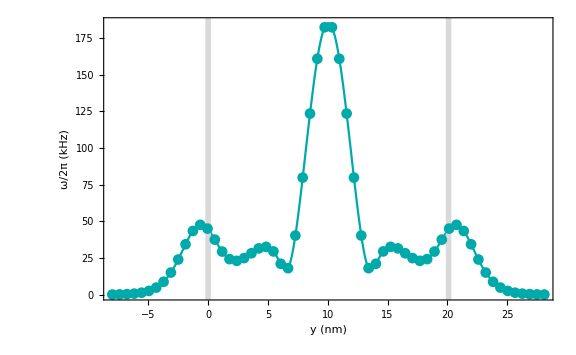

```mathematica
ListLinePlot[Table[{x[[i]],Total[MANRImpureCoupleFreq[[79]]][[i]]},{i,1,Length[x]}],PlotMarkers->Automatic,InterpolationOrder->3,PlotTheme->"Scientific",FrameStyle->Thickness[0.005],GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],ImageSize->Large,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->32}],PlotStyle->Directive[Darker[Cyan]],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotRange->All]
```

# SCQ-Magnon Coupling in MZNRs

## Coupling

```mathematica
MZNRCoupleFreq=DeleteCases[Table[Import["MZNR_couple_data/MZNR_pure_couple_w="<>ToString[j]<>".mx"],{j,2.9,3.2,0.01}],_?FailureQ];//Quiet
```

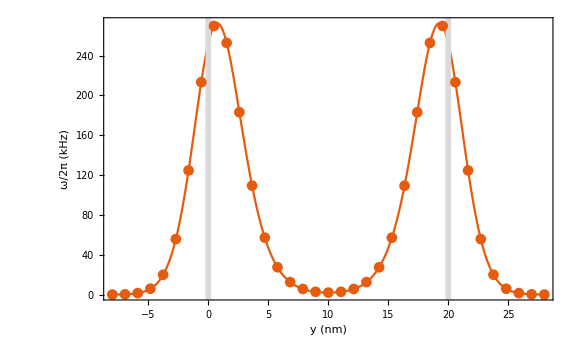

```mathematica
NSteps=34;
l=((3/2)*(NSteps)-1)*a;
x=Table[-20+j*N[(l/a+40)/NSteps],{j,0,NSteps}]*0.4;
ListLinePlot[Table[{x[[i]],Total[MZNRCoupleFreq[[28]]][[i]]},{i,1,Length[x]}],PlotMarkers->Automatic,InterpolationOrder->3,PlotTheme->"Scientific",FrameStyle->Thickness[0.005],GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],ImageSize->Large,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->32}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotRange->All]
```

## Coupling Density

```mathematica
TotalMZNRCoupleFreq =Table[Total[MZNRCoupleFreq[[i]]],{i,1,Length[MZNRCoupleFreq]}];
ListDensityPlot[TotalMZNRCoupleFreq ,PlotRange->All]
```

-Graphics-

# Paper Figures